# The Last Derivative Rules

## y=ⅇ^x

A very interesting thing happens with f(x)=ⅇ^x and its derivative:

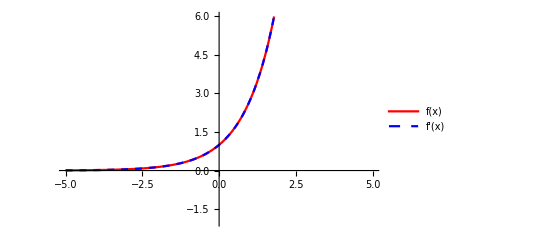

```mathematica
f[x_]:=ⅇ^x;
Plot[{f[x],f'[x]},{x,-5,5},PlotRange->{-2,6},PlotStyle->{{Red,Thick},{Blue, Dashed}},PlotLegends->"Expressions"]
```

According to the graph above, what is the derivative of y=ⅇ^x?

d/dx(ⅇ^x) =

Check your answer with Mathematica. Note: you need to use the palette to get the correct ⅇ, otherwise, e will be treated as a variable:

```mathematica
D[ⅇ^x,x]
```

## y=ln(x)

Here is a graph of g(x)=ln(x) and its derivative:

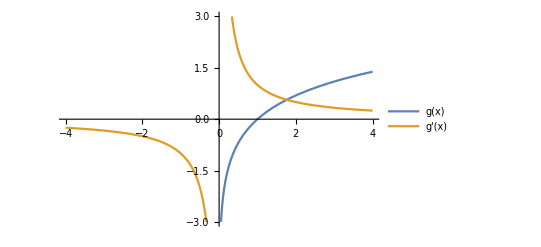

```mathematica
g[x_]:=Log[x];
Plot[{g[x],g'[x]},{x,-4,4},PlotRange->{-3,3},PlotLegends->"Expressions"]
```

This derivative graph is one you are familiar with. What is the derivative of y=ln(x)?

d/dx ln(x) =

Check your answer with Mathematica. Note: in Mathematica, you need to enter ln(x) as Log[x].

```mathematica
D[Log[x],x]
```

#### A note about Domain:

While the graph above shows the derivative of ln(x) defined for x<0, it should only be defined for x>0 since the domain of ln(x) is x>0. Technically, Mathematica is incorrect and should only graph the right side!

## Using the Chain Rule

The “official” versions of these derivative rules apply the Chain Rule:

d/dx(ⅇ^u)=ⅇ^u·u'   and   d/dx ln(u)=1/u·u'

#### Several Short Examples:

y=ⅇ^(5x)
y'=5 ⅇ^(5x)

f(x)=ⅇ^(x^2-3x)
f'(x)=(2x-3)ⅇ^(x^2-3x)

y=ln(5 x^3)
y'=1/(5 x^3)(15 x^2)
y'=5/x

h(x)=ln(x^2-1)
h'(x)=1/(x^2-1)(2x)
h'(x)=(2x)/(x^2-1)

## Bases Besides e

Similar rules can be found for bases other than ⅇ, such as a constant, a :

d/dx(a^x)=a^x·ln(a)

d/dx log_a(x)=1/x·1/a

### Comparing the Derivative Rules with the Chain Rule:

#### Several Short Examples:

y=5^(3 x^2)
y'=6x·5^(3 x^2)·ln(5)

f(x)=log(3x-5)       (log base 10)
f'(x)=1/(3x-5)·1/(ln(10))

## Derivatives of Inverse Trig Functions

It is much harder to guess the derivatives of the inverse trig functions, like  y=sin^-1(x) and y=cos^-1(x).
Fortunately, Mathematica can quickly calculate these derivative rules for us:

```mathematica
D[ArcSin[x],x]
```

1/(√(1-x^2))

```mathematica
D[ArcCos[x],x]
```

-1/(√(1-x^2))

Continuing this process, here are all six:

```mathematica
-Graphics-    -Graphics-
```

## Mixed Practice

### One

Find dy/dx for y=ⅇ^(x^2)tan(3x):

Check your answer with Mathematica.

### Two

Find f'(x) for f(x)=ln(5x)·tan^-1(x^3-1) :

Check your answer with Mathematica.

### Three

Find dy/dx for y=ⅇ^(x^2)tan(3x) :

Check your answer with Mathematica.

### Four

Find g'(x) for g(x)=ln(x)cos^-1(4x) :

Check your answer with Mathematica. You can use the following format to combine the terms into one fraction:
D[□,var]//Together

### Five

Find h'(x) for h(x)=(ln(x))/ⅇ^x :

Check your answer with Mathematica.

## Authorship Information

Dan Uhlman
uhlmand@tas.tw